## Solving the k=0 case

You don’t need to worry about the X(x) solution. It is the one with the eigenfunctions and the one that allowed us to have k=0 as an answer so we will only talk about the Y(y) solution.

Going back to the separted ODE we have:

Y''(y)-k^2 Y(y)=0

Setting k=0 we get:

Y''(y)=0

This can be solved with any general first order polynomial. We will call it

y = my+b

Where m and b are arbitrary constants.

As we did earlier in this problem we will write y as L_y-y and reform this solution to be the following:

y = m̃(L_y-y) + b̃

Where the “ ~’s “ represent any changes to the constant terms that are needed in the L_y-y substitution.

We then apply the BC y(30)=0

m̃(30 - 30) + b̃ =0 → b̃=0

y = m̃(L_y-y)

Now we will turn to the y=0 boundary condition that y(0) = f(x), where f(x)=x and f(x) =100

### The f(x)=100 case

We still have the solution:

y = m̃(L_y-y)

Applying the y(0)=100 we have:

m̃(L_y-0) = 100

m̃ = 100/L_y = 100/30 = 10/3

You should have found that for the k ≠ 0 case there are no solutions when f(x) =100 (evaluating the integral for E_nshould have led youto E_n=0 ∀ n ≥ 1

This means that the entire solution for the f(x) =100 case is

T(x,y) = 10/3(L_y-y) = 10/3(30-y)

Here are some plots of these solutions when n=1, 2, 5, 10, 35, and 100

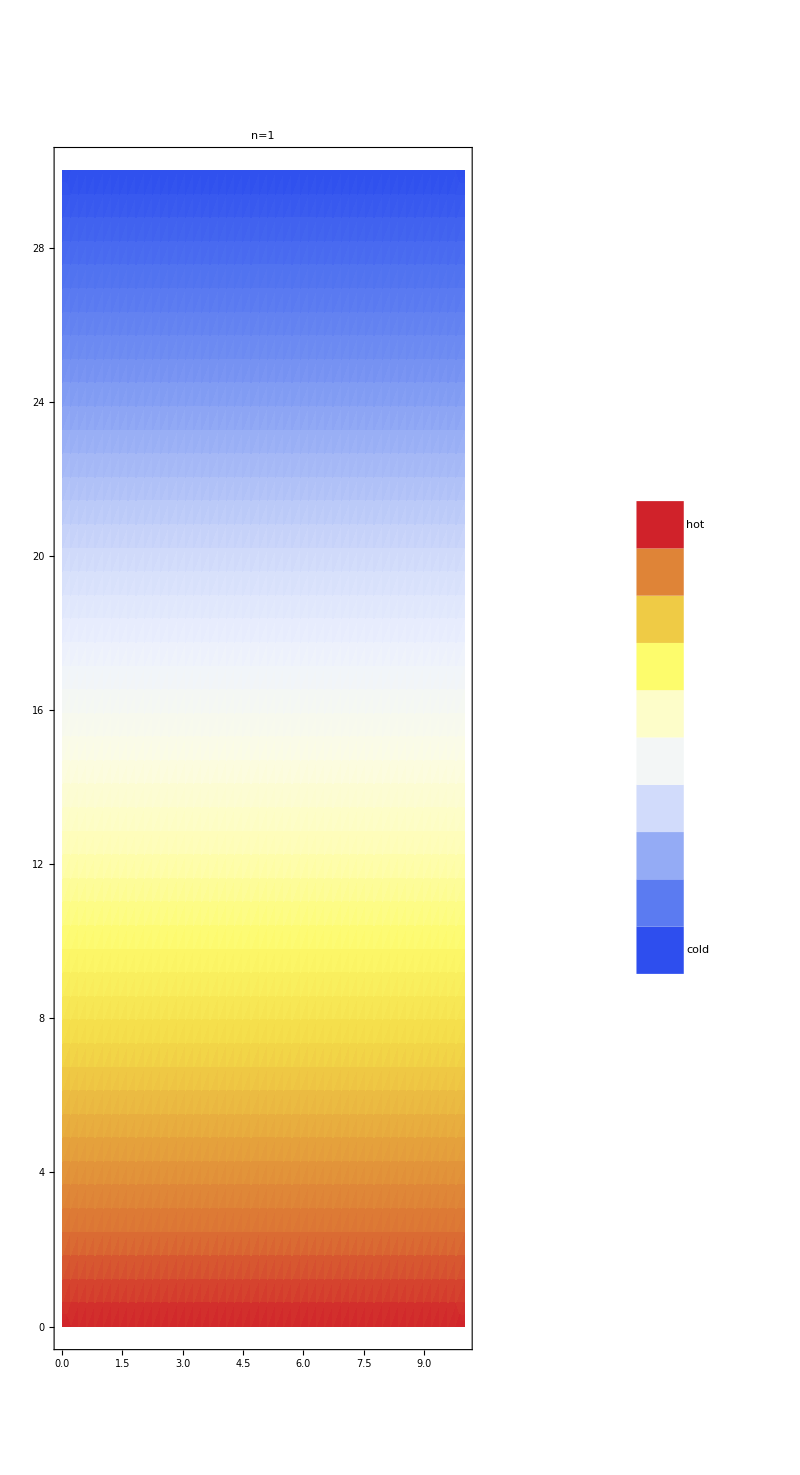
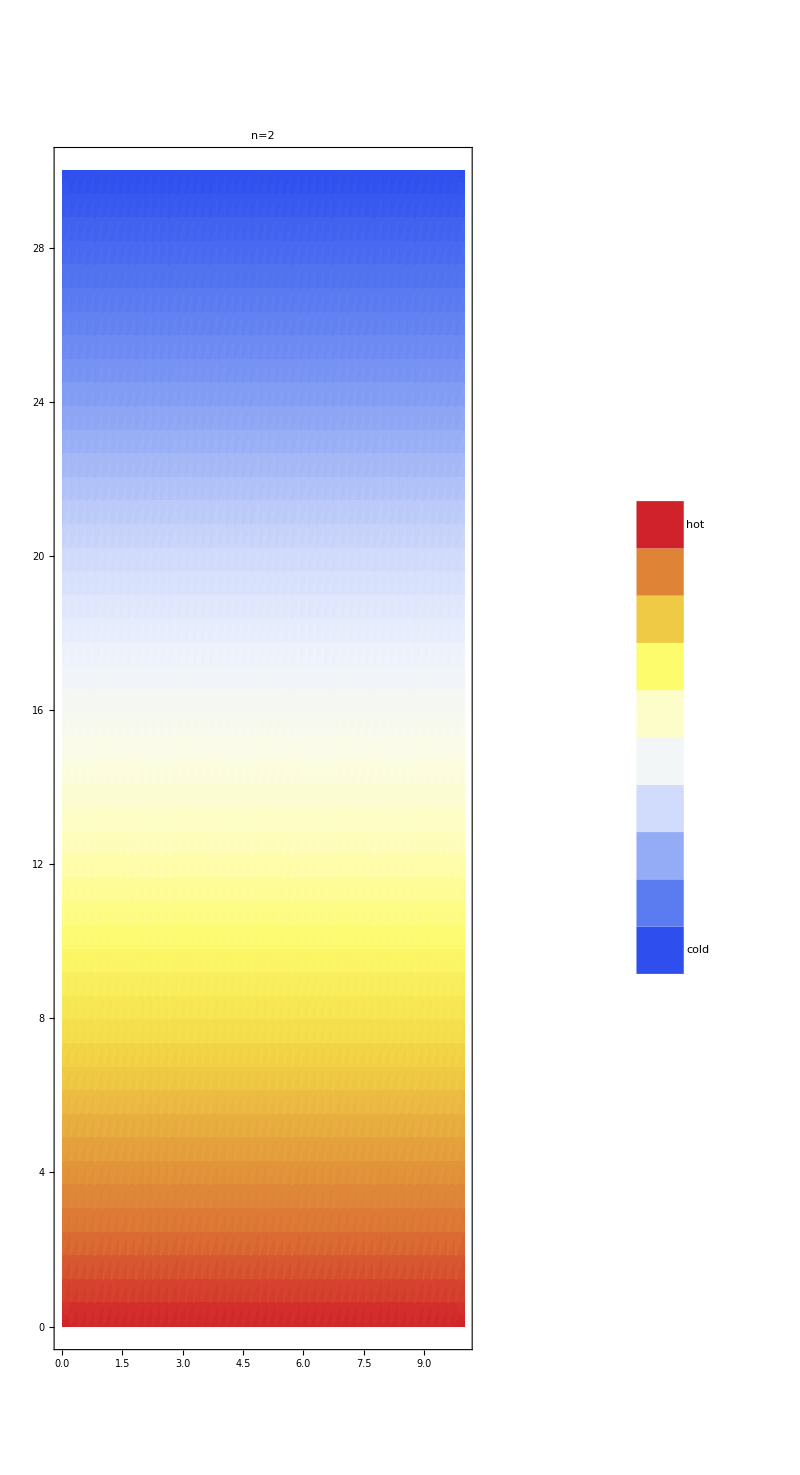
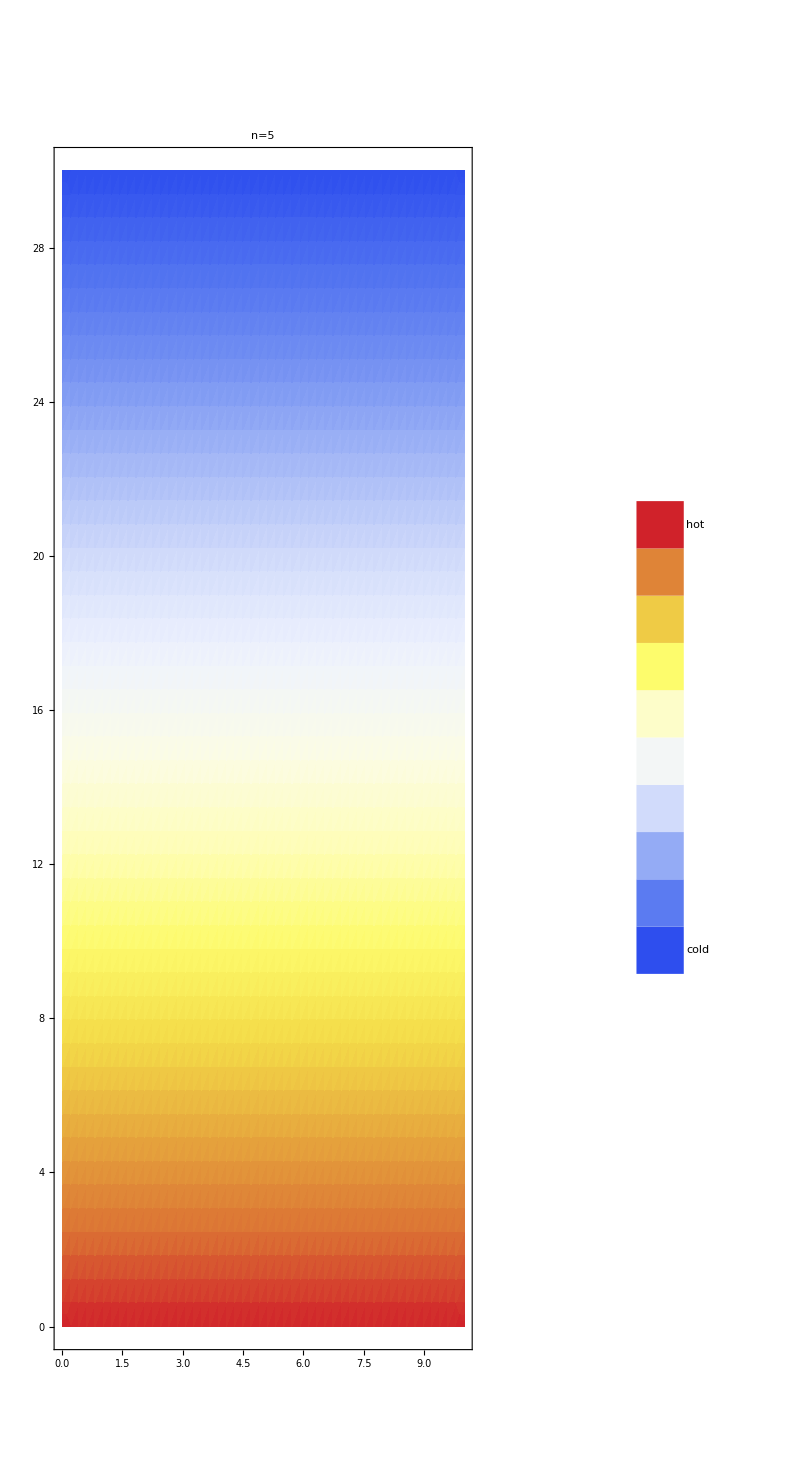
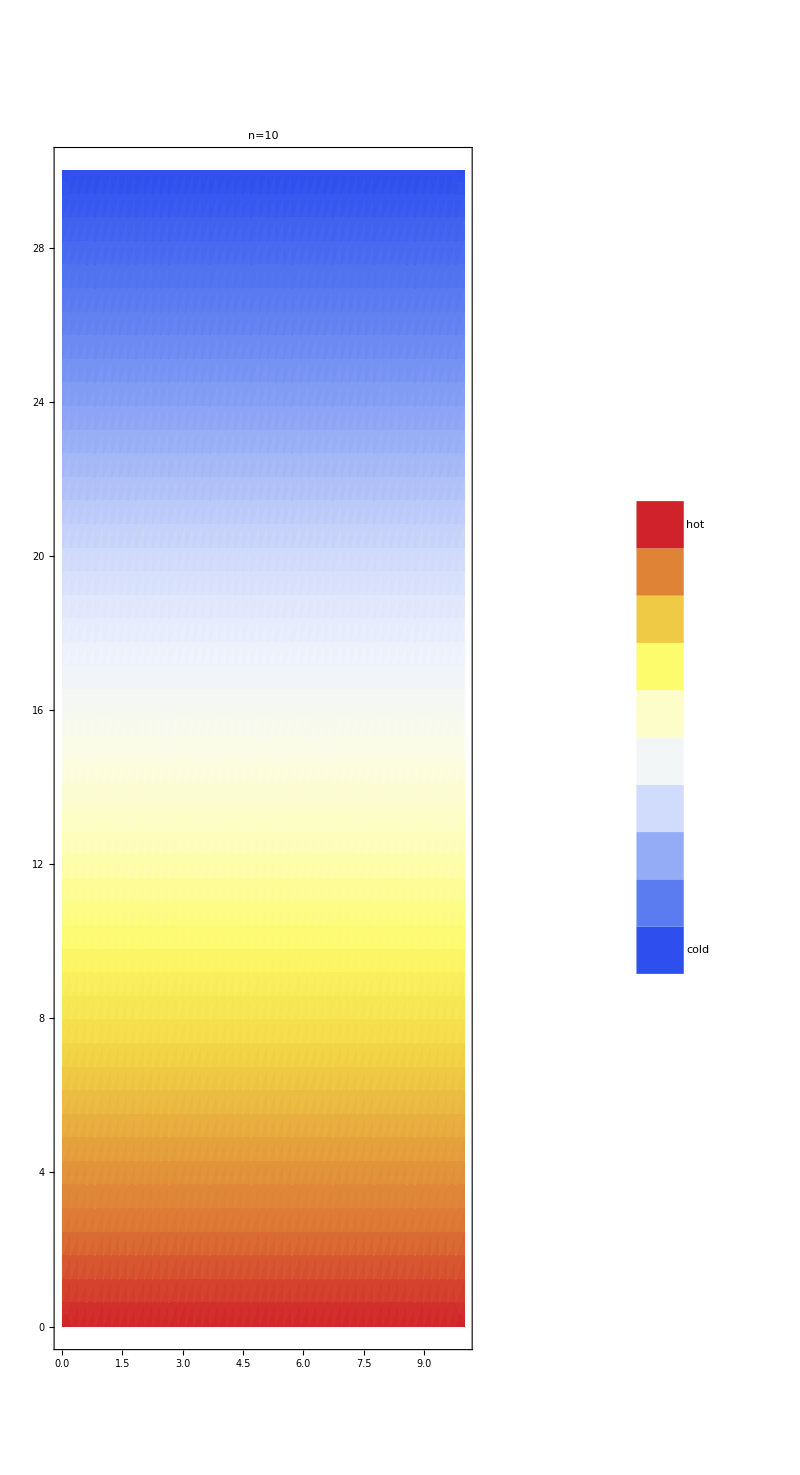
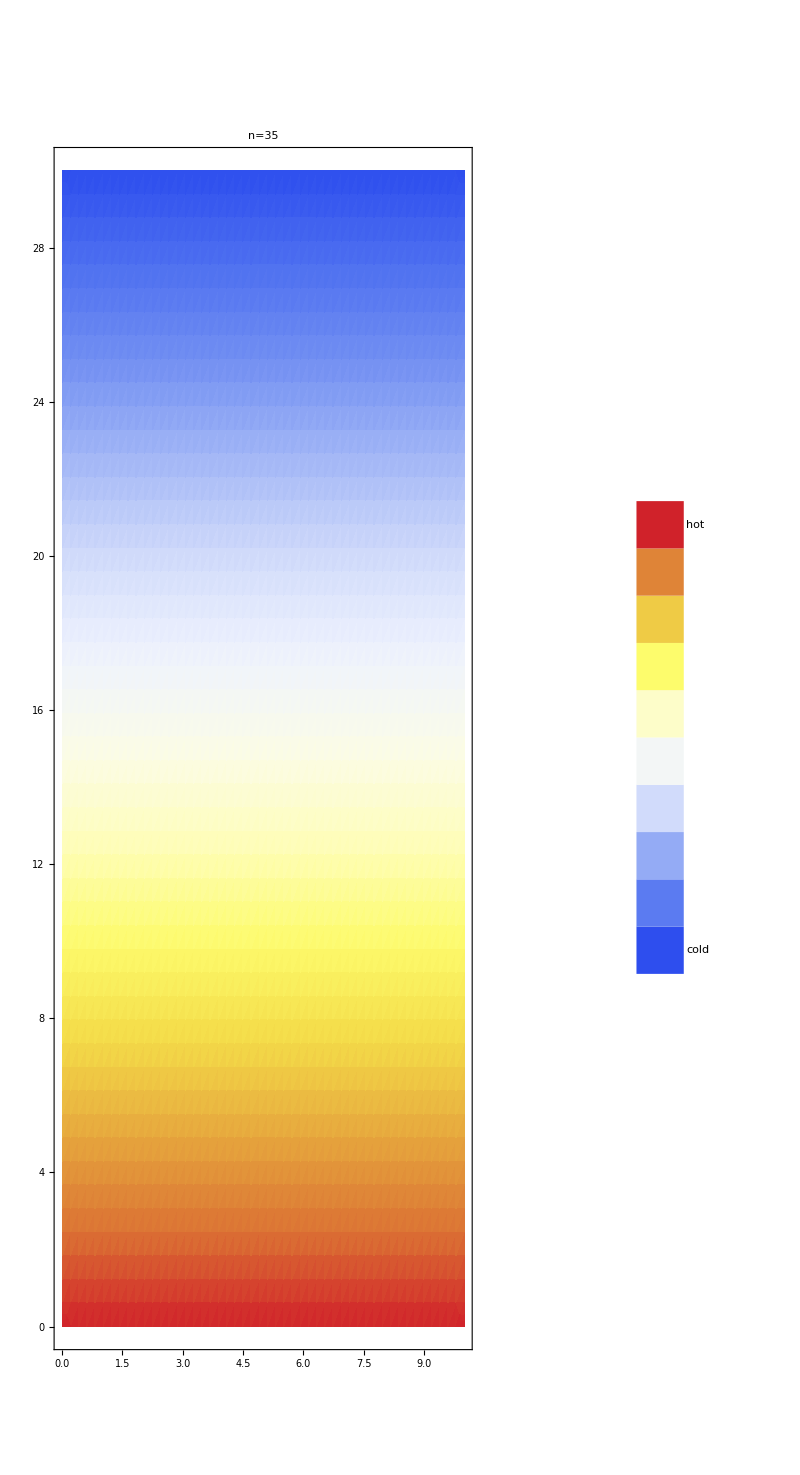
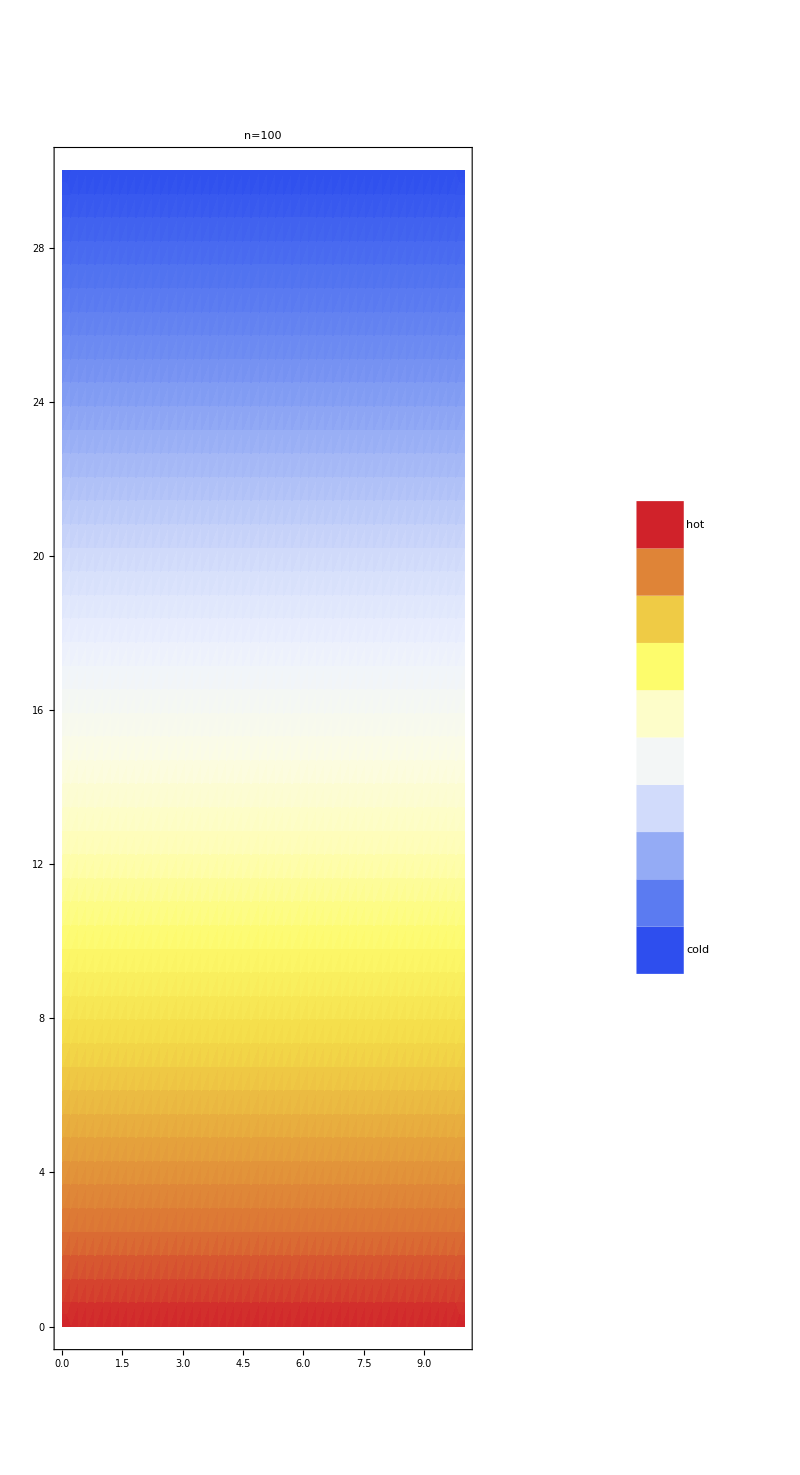

### The f(x)=x Case

Again we start with our solution:

y = m̃(L_y-y)

Applying the BC y(0)=x we have

m̃(L_y-0) = x

m̃ 30 = x

Now is the tricky part. We want to solve for an absolute m̃, or one that doens’t depend on x. Do to this we are going to integrate both sides with respect to x across all x in our problem. That mens the limits of integration on both sides are from 0 to L_x.

∫_0^L_x m̃ 30ⅆx = ∫_0^L_x x ⅆx

(m̃ 30 x )|L_x
0 =(  x^2/2)|L_x
0

30 m̃ (L_x-0) = (L_x^2/2 - 0^2/2)

30 m̃ L_x = L_x^2/2

m̃ = L_x/(2 *30) = 10/60 = 1/6

The solution for f(x)=x and k=0 is

y = 1/6(L_y-y) = 1/6(30-y)

Now the entire solution when f(x) = x  becomes:

T(x,y) = 1/6(30-y) - 40/π^2∑_(n=1)^∞ 1/((2n-1)^2 sinh (3 π (2n-1)))sinh (((2n -1) π)/10(30-y)) cos (((2n-1)  π x)/10)

Here are some plots of these solutions when n=1, 2, 5, 10, 35, and 100